```mathematica
radius=Import[path~~"radius.log","Table"];
avmass=Import[path~~"avmass.log","Table"];
```

```mathematica
path="/Users/wanglong/task/fall/MM/";
rlabel=Import[path~~"rlabel.log","Table"]
adjust=Import[path~~"adjust.log","Table"];
rlagr=Import[path~~"rlagr.log","Table"];
rlagrlable=ToString/@{T,1,2,5,10,20,30,40,50,70,90,100};
scale=Import[path~~"scale.log","Table"][[1]]
```

{{<R>,RTIDE,RDENS,RC,NC,MC,RHOD,RHOM,CMAX,<Cn>,Ir/R,UN,NP,RCM,VCM,AZ,EB/E,EM/E,TCR,T6,NESC,VRMS}}

{R*,1.,M*,122033.,V*,22.91,T*,0.043,<M>,0.48,SU,4.4×10^7}

```mathematica
Length/@{radius,adjust}
```

{67,67}

```mathematica
rc=Table[{adjust[[i,5]],radius[[i,5]]},{i,Length@adjust}];
rcreal=Table[{adjust[[i,5]]*scale[[8]],radius[[i,5]]*scale[[2]]},{i,Length@adjust}];
q=adjust[[All,{5,11}]];
qreal=Table[{adjust[[i,5]]*scale[[8]],adjust[[i,11]]},{i,Length@adjust}];
```

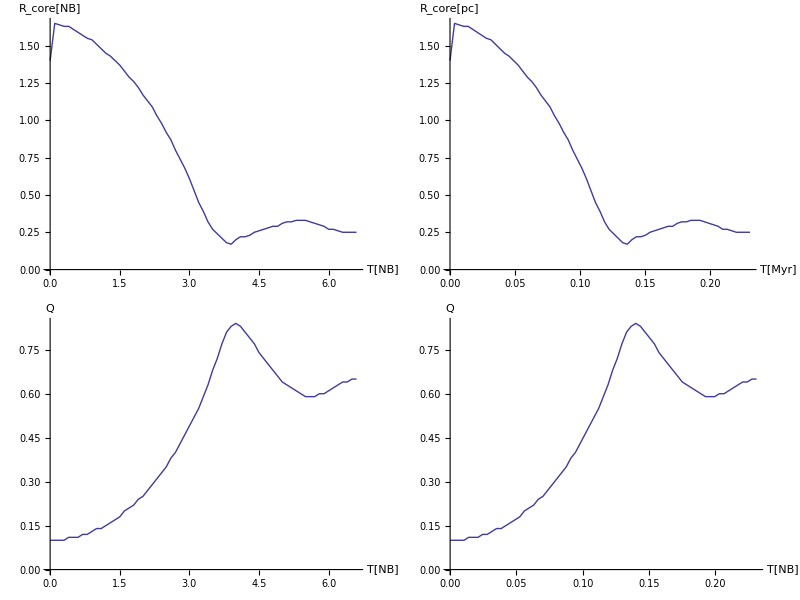

```mathematica
out=Grid[{{ListPlot[rc,AxesLabel->{"T[NB]","R_core[NB]"},Joined->True,ImageSize->400],ListPlot[rcreal,AxesLabel->{"T[Myr]","R_core[pc]"},Joined->True,ImageSize->400]},{ListPlot[q,AxesLabel->{"T[NB]","Q"},Joined->True,ImageSize->400],ListPlot[qreal,AxesLabel->{"T[NB]","Q"},Joined->True,ImageSize->400]}}]
```

```mathematica
larg[data_,label_,scalej_,title_,range_]:=ListPlot[Table[{data[[i,1]]*scale[[8]],data[[i,j]]*scalej},{j,{3,5,6,10,13}},{i,Length@rlagr}],Joined->True,AxesLabel->{"T[Myr]",label},
PlotLegends->rlagrlable[[{2,4,5,9,12}]]"%M_tot",PlotLabel->title,PlotRange->range,PlotStyle->Table[RGBColor[i/5,0,1-i/5],{i,5}],ImageSize->500,PlotRange->Full]
```

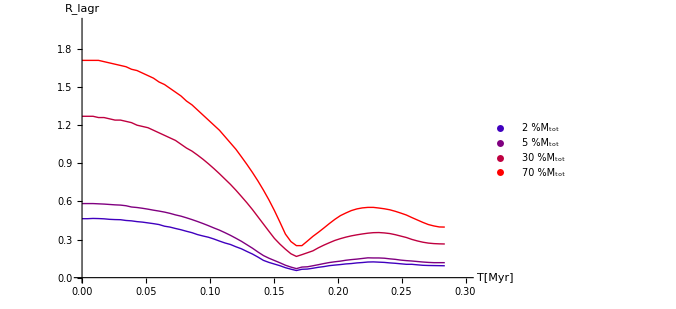

```mathematica
out=larg[rlagr,"R_lagr",1,"",{{0,0.3},{0,2}}]
```

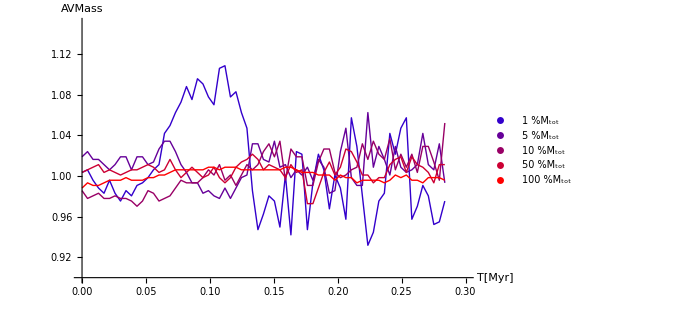

```mathematica
out=larg[avmass,"AVMass",256000,"",{{0,0.3},{0.9,1.15}}]
```

```mathematica
Export["/Users/wanglong/Downloads/Result.pdf",out]
```

/Users/wanglong/Downloads/Result.pdf

```mathematica
Clear[larg]
```